```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
ufun=NDSolveValue[{D[u[x,t],{t,2}]==4* D[u[x,t],{x,2}],
u[0,t]==0,u[1,t]==0,u[x,0]==Sin[π x],Derivative[0,1][u][x,0]==0},
u,{x,0,1},{t,0,3}];
Plot3D[ufun[x,t],{x,0,1},{t,0,3},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

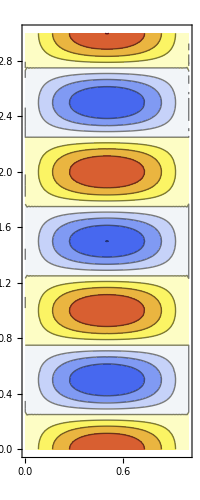

```mathematica
ContourPlot[ufun[x,t],{x,0,1},{t,0,3},ColorFunction->"Temperature",AspectRatio->Automatic]
```

```mathematica
Plot3D[Sin[π x] Cos[2 π t],{x,0,1},{t,0,3}]
```

-Graphics3D-

```mathematica
ufun=NDSolveValue[{D[u[x,t],{t,2}]==4* D[u[x,t],{x,2}],
u[0,t]==0,u[1,t]==4,u[x,0]==0,Derivative[0,1][u][x,0]==0},
u,{x,0,1},{t,0,3}];
Plot3D[ufun[x,t],{x,0,1},{t,0,3},ColorFunction->"TemperatureMap"]
```

NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolveValue::eerr: Warning: scaled local spatial error estimate of 141.577 at t = 3. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

-Graphics3D-